```mathematica
Ln=4;
```

P(l<L)

```mathematica
P1[l_,p_]:=(1-p)* p^l
```

P(l=L)

```mathematica
P2[L_,p_]:=p^L
```

Ordered Entropy

```mathematica
EN[L_,p_]:=-(Sum[P1[l,p]*Log[P1[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

Cyclic Entropy

```mathematica
ENC[p_]:=-(Log[1-p]+p/(1-p)*Log[p])
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

Perfect Clock P(l<L)

```mathematica
PC[l_,τ_]:=(τ^l)/(l!)*ⅇ^-τ
```

Perfect Clock P(l=L)

```mathematica
PCM[L_,τ_]:=1-Sum[(τ^l)/(l!)*ⅇ^-τ,{l,0,L-1}]
```

Entropy of Totally Ordered RXN with perfect clock

```mathematica
ENP[L_,τ_]:=-(Sum[PC[l,τ]*Log[PC[l,τ]],{l,0,L-1}]+PCM[L,τ]*Log[PCM[L,τ]])
```

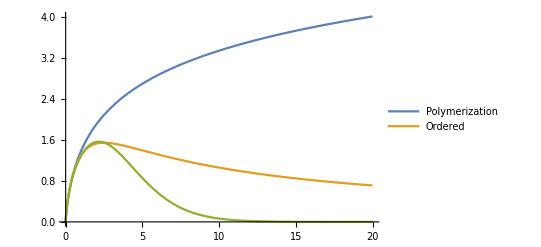

```mathematica
Plot[{ENC[h[τ]],EN[Ln,h[τ]],ENP[Ln,τ]}, {τ,0,20},PlotLegends->{"Polymerization","Ordered"}]
```

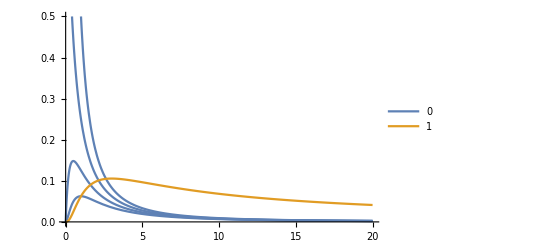

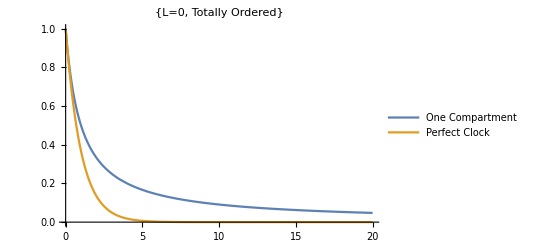

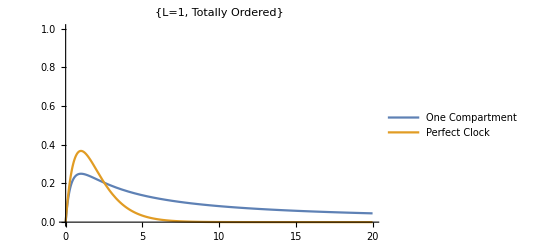

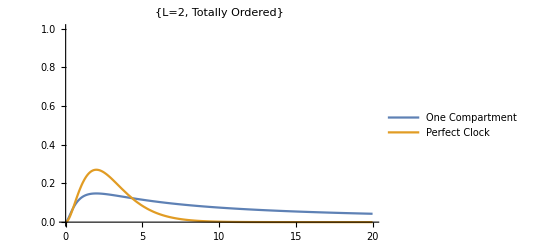

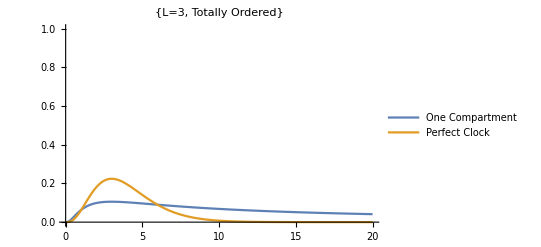

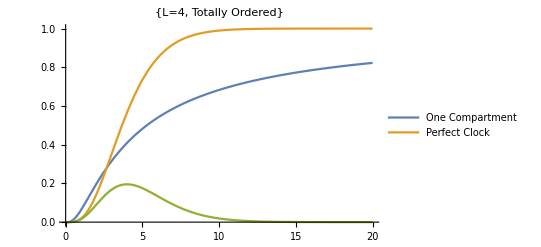

```mathematica
T=Evaluate@Table[P1[l,h[τ]],{l,0,Ln-1}];
T2=Evaluate@Table[PC[l,τ],{l,0,Ln}];
Plot[{T/τ, P2[Ln,h[τ]]/τ},{τ,0,20},PlotRange->{0,0.5},PlotLegends->{"0" ,"1","2","3","4"}]
Plot[{T[[1]],T2[[1]]},{τ,0,20},PlotLegends->{"One Compartment","Perfect Clock"},PlotLabel->{"L=0, Totally Ordered"},PlotRange->{0,1}]
Plot[{T[[2]],T2[[2]]},{τ,0,20},PlotLegends->{"One Compartment","Perfect Clock"},PlotLabel->{"L=1, Totally Ordered"},PlotRange->{0,1}]
Plot[{T[[3]],T2[[3]]},{τ,0,20},PlotLegends->{"One Compartment","Perfect Clock"},PlotLabel->{"L=2, Totally Ordered"},PlotRange->{0,1}]
Plot[{T[[4]],T2[[4]]},{τ,0,20},PlotLegends->{"One Compartment","Perfect Clock"},PlotLabel->{"L=3, Totally Ordered"},PlotRange->{0,1}]
Plot[{P2[Ln,h[τ]],PCM[Ln,τ],T2[[5]]},{τ,0,20},PlotLegends->{"One Compartment","Perfect Clock"},PlotLabel->{"L=4, Totally Ordered"},PlotRange->{0,1}]
```

```mathematica
T2=Evaluate@Table[τ/.Solve[P1[i,h[τ]]==1/20&& τ>0],{i,0,Ln+4}]
```

{{19},{9-4 √5,9+4 √5},{Root[1+3 #1-17 #1^2+#1^3&,2],Root[1+3 #1-17 #1^2+#1^3&,3]},{Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,1],Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,2]},{Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,2],Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,3]},{Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,1],Root[1+6 #1+15 #1^2+20 #1^3+15 #1^4-14 #1^5+#1^6&,2]},{Root[1+7 #1+21 #1^2+35 #1^3+35 #1^4+21 #1^5-13 #1^6+#1^7&,2],Root[1+7 #1+21 #1^2+35 #1^3+35 #1^4+21 #1^5-13 #1^6+#1^7&,3]},τ,τ}

```mathematica
L1=τ/.Solve[P2[Ln,h[τ]]==1/20&&τ>0]
```

{Root[-1-4 #1-6 #1^2-4 #1^3+19 #1^4&,2]}

```mathematica
a[x_]:=1/;L1[[1]]<x
b[x_]:=0.2/; x<T2[[1]][[1]]
c[x_]:=0.4/;T2[[2]][[1]]<x<T2[[2]][[2]]
d[x_]:=0.6/;T2[[3]][[1]]<x<T2[[3]][[2]]
e[x_]:=0.8/;T2[[4]][[1]]<x<T2[[4]][[2]]
f[x_]:=1/;T2[[5]][[1]]<x<T2[[5]][[2]]
g[x_]:=1.2/;T2[[6]][[1]]<x<T2[[6]][[2]]
i[x_]:=1.4/;T2[[7]][[1]]<x<T2[[7]][[2]]
```

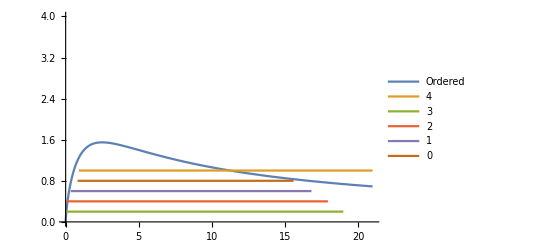

```mathematica
Plot[{EN[Ln,h[x]],a[x],b[x],c[x],d[x],e[x]},{x,0,21},PlotRange->{0,4},PlotLegends->{"Ordered","4","3","2","1","0"}]
```

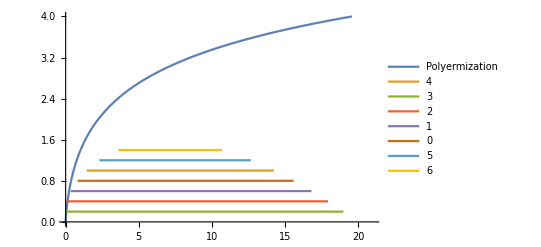

```mathematica
Plot[{ENC[h[x]],f[x],b[x],c[x],d[x],e[x],g[x],i[x]},{x,0,21},PlotRange->{0,4},PlotLegends->{"Polyermization","4","3","2","1","0","5","6"}]
```